```mathematica
(*Form for density of characteristic (1-bx^2), 0 < b < 1*)
Clear[b]
Clear[b1]
Clear[b2]
Clear[a1]
Clear[a2]
L[x_,b_] = 1/(Sqrt[2*Pi]) *(1-b+b x^2) E^(-x^2/2)
dist = ProbabilityDistribution[L[x],{x,-Infinity,Infinity}]
```

(ⅇ^(-x^2/2) (1-b+b x^2))/(√(2 π))

ProbabilityDistribution[x^4 ⅇ^(-x^2/2),{x,-∞,∞}]

```mathematica
f[y_,a1_,a2_,b1_,b2_] = Integrate[(1/Sqrt[a1*a2])*L[x/(Sqrt[a1]),b1]*L[(y-x)/Sqrt[a2],b2],{x,-Infinity,Infinity}]
```

ConditionalExpression[-(a1 a2 ⅇ^(-y^2/(2 (a1+a2))) ((a1+a2)^2 (-(a1+a2)^2+a1 (a1+a2) b1+a2 (a1+a2-3 a1 b1) b2)-(a1+a2) (a1 (a1+a2) b1+a2 (a1+a2-6 a1 b1) b2) y^2-a1 a2 b1 b2 y^4))/(√(1/a1+1/a2) (a1 a2)^(3/2) (a1+a2)^4 √(2 π)), Re[1/a1+1/a2]≥0]

```mathematica
f[y_,a1_,a2_,b1_,b2_] = -((a1 a2 ⅇ^(-y^2/(2 (a1+a2))) ((a1+a2)^2 (-(a1+a2)^2+a1 (a1+a2) b1+a2 (a1+a2-3 a1 b1) b2)-(a1+a2) (a1 (a1+a2) b1+a2 (a1+a2-6 a1 b1) b2) y^2-a1 a2 b1 b2 y^4))/(√(1/a1+1/a2) (a1 a2)^(3/2) (a1+a2)^4 √(2 π)))
```

-((a1 a2 ⅇ^(-y^2/(2 (a1+a2))) ((a1+a2)^2 (-(a1+a2)^2+a1 (a1+a2) b1+a2 (a1+a2-3 a1 b1) b2)-(a1+a2) (a1 (a1+a2) b1+a2 (a1+a2-6 a1 b1) b2) y^2-a1 a2 b1 b2 y^4))/(√(1/a1+1/a2) (a1 a2)^(3/2) (a1+a2)^4 √(2 π)))

0.5

0.5

0.3

0.7

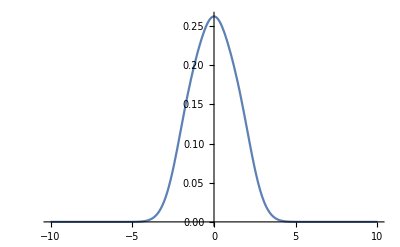

```mathematica
Plot[f[y,.5,.5,.3,.7],{y,-10,10}]
```

```mathematica
(*Investigating p ≥ 2 regime via Tkocz low convexity method, for a lower bound*)
```

```mathematica
pth[p_,b_] = Integrate[x^p*L[x,b],{x,-Infinity,Infinity}]
```

ConditionalExpression[(2^(-1/2+1/2 (-1+2 b+p)) (1+(-1)^(2 b+p)) Gamma[1/2+b+p/2])/(√π), Re[2 b+p]>-1]

```mathematica
Lnpb[x_,p_,b_]= L[x/pth[p,b],b]/pth[p,b]
```

ConditionalExpression[(2^(1/2 (1-2 b-p)) ⅇ^(-(2^(1-2 b-p) π x^2)/((1+(-1)^(2 b+p))^2 Gamma[1/2+b+p/2]^2)) π^b ((2^(1/2+1/2 (1-2 b-p)) x)/((1+(-1)^(2 b+p)) Gamma[1/2+b+p/2]))^(2 b))/((1+(-1)^(2 b+p)) Gamma[1/2+b+p/2]), Re[2 b+p]>-1]

```mathematica
(*Which is clearly convex*)
```

Expectation::argmu: Expectation called with 1 argument; 2 or more arguments are expected.